```mathematica
sp500 = Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\Data\\TSLA daily log return.csv"]];
return = sp500[[3]];
return = Delete[return,1];
return = Delete[return,1];
FindDistributionParameters[return,TsallisQGaussianDistribution[μ,β,q]]
FindDistributionParameters[return,NormalDistribution[μ, σ]]
```

{μ→0.00183861,β→0.0172022,q→1.56554}

{μ→0.00183861,σ→0.067919}

```mathematica
returnsquared = return^2;
```

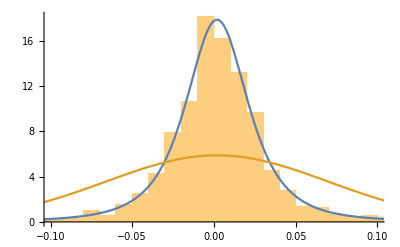

```mathematica
Show[Histogram[return,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[0.001838613476592,0.017202,1.565],x],PDF[NormalDistribution[0.001838613476592,0.06791],x]},{x,-0.15,0.15}]]
```

```mathematica
qVar[μ_, β_, q_] :=Variance[TsallisQGaussianDistribution[μ,β,q]]
Var[μ_, σ_]:=Variance[NormalDistribution[μ,σ]]
qDrift[μ_, β_,q_]:=μ+qVar[μ, β, q]/2
Drift[μ_,σ_]:=μ+Var[μ, σ]/2
qVolatility[μ_,β_, q_]:=√qVar[μ, β, q]
Volatility[μ_,σ_]:=√Var[μ, σ]
```

```mathematica
qVolatility[0.00183861,0.017202, 1.565]
Volatility[0.0018386,0.0679]
```

0.0440498

0.0679

```mathematica
qDrift[0.00183861,0.017202, 1.565]
Drift[0.0018386,0.0679]
```

0.0028088

0.00414381

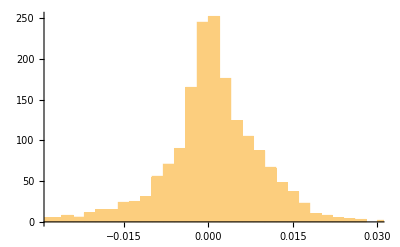

```mathematica
Histogram[return]
```

```mathematica
p =Transpose[Import["C:\\Users\\Eakka\\Documents\\GitHub\\Trading-in-qGaussian\\SatT.csv"]];
p =p[[2]];
p = Delete[p, 1];
```

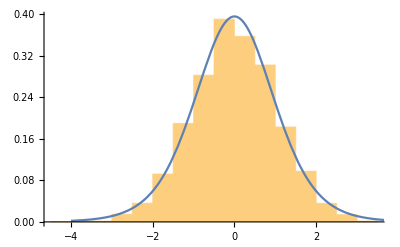

```mathematica
Show[Histogram[p,Automatic,"ProbabilityDensity"],Plot[{PDF[TsallisQGaussianDistribution[0.00039,0.931032512,1.2],x]},{x,-4,4}]]
```

```mathematica
√(1/(2*0.57682))
```

0.931033

```mathematica
Variance[TsallisQGaussianDistribution[μ,β,q]]
```

Piecewise[{{(2 β^2)/(5-3 q), q<5/3}, {∞, 5/3≤q<2}, {Indeterminate, True}}]